# Mathematica Tutorial 1 Your name: Bella Falbo

From Introduction to Computational Science:  Modeling and Simulation for the Sciences
Angela B. Shiflet and George W. Shiflet Wofford College,  Tutorial © 2009
With modifications by C. Golé, Smith College - last updated Jan 2024

This first tutorial on Mathematica gives an introduction to the system and prepares you to use it to complete projects. It goes through basic functions of Mathematica, and has you practice  with Quick Review Questions (QRQ). 

Once done, upload the file to the Google folder in your name that I shared with you, and start writing, in a  google doc named “Portfolio Your Name” in the same folder, some comments about what you learned in this tutorial, and how it relates to your previous experience in math or computer science.

## 1. Getting Started

Mathematica is a powerful computer algebra system that can plot graphs and perform a large variety of calculations with symbols as well as numbers. A Mathematica notebook, such as this one, is like an interactive book with text and the capability of performing calculations and manipulations.

To open this notebook, you probably double-clicked the Mathematica folder to open it and then double-clicked the Mathematica icon to start a new notebook or double-clicked this file, MathematicaTutorial1.nb.

If you do not see a palette on the right with symbols, such as the square root sign, go to the Palettes menu and select Classroom Assistant.   

The material in a notebook is separated into cells, which are marked with a right square bracket.  Cells have different tasks, such as input, output, and text.  In the following material, evaluate each given expression in an input cell. To evaluate an expression, with the cursor anywhere in its cell press <ENTER> on the numeric keypad (not <ENTER> or <RETURN> on the main keyboard) or <SHIFT>-<ENTER> or click Enter in the Classroom Assistant menu.  Execute all input cells to view the results of the examples.  Input is labeled with In, and output is labeled with Out.  The number in square brackets indicates the calculation order of the expression.  We start by evaluating 25 factorial, which is the product of the positive integers from 1 through 25, using the exclamation mark ! as in mathematics:

```mathematica
25!
```

15511210043330985984000000

The following is the first of the Quick Review Questions  (QRQ) that you will have to show in your completed tutorial.

#### Quick Review Question (QRQ) 1.1 Because cells as this one are text cells and not input cells, do not type in these cells. Instead, move the cursor down until it changes from being vertical to being a horizontal-I bar. Click and start typing; a new input cell will form. For this question, evaluate 100-factorial.

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

## 2. Save

Save what you have done by going to the File menu and choosing Save or Save As....  The first time you save a new file, make sure you save the file to your external storage using a descriptive name. You can also use Save to cloud if you plan to toggle between computers, and share a document with a team. 

After you have saved initially, you can just go to the File menu and select Save or use the short cut indicated under that menu.  SAVE OFTEN, particularly before you print, do a long calculation, or display a graph.

#### QRQ 2.1 Save this notebook on your disk. How did you accomplish this task? File, save. (If you have access to Wolfram Cloud, you can use “File/Save to cloud” to use the file in another machine)

## 3. Additional Features

We can select text from a cell and cut, copy, or paste it using items from the Edit menu or the short cuts indicated on that menu.  We can also select a cell by clicking on the bracket on the right of the screen; we can then cut, copy, or paste the cell.

#### QRQ 3.1 Select this cell and move it above the preceding cell and back.

To type text before starting a cell, choose the style Text or another heading or section style from Style in the Format menu or from the top left of the notebook.  Note the keyboard shortcut in the menu (Command-7 for Apple, Ctrl-7 for Windows). A cell in Text style is for documentation and does not execute.  If you have already started typing and wish to change the style, click the cell bracket and choose the style.  The default type is Input.

QRQ 3.2 Change the style of this cell to text style.

Other useful advice
- If you are in one cell, to start another cell, move the mouse down until you get a horizontal I-bar and click.
- To quit Mathematica, choose Quit from the File menu or use the indicated short cut.
- If a computation is stuck for any reason (it will happen) try Command-. (that’s a period) in a IOS, Ctrl-. in Windows. If this does not work, go to the menu Evaluation/Quit Kernel/Local.
- If you quit and re-open a notebook later, you must re-execute any function definition or variable assignment to use it again.

## 4. Wolfram Alpha is within Mathematica

You may have used Wolfram Alpha, the online calculator, when studying Calculus, or other math subjects. Stephen Wolfram is the inventor of Mathematica, and Wolfram Alpha is an online service whose engine is Mathematica, working on a bank of servers somewhere. You can use Wolfram Alpha right off Mathematica by starting your command by an equal sign. The advantage is that, for the most part,  Wolfram alpha is not a syntax snob. So you can write  in plain English. Mathematica connects to the web, Wolfram Alpha decodes your query, translates it into a Mathematica command and executes it. In the process you can learn and copy the Mathematica command. Start with an = sign a Wolfram Alpha query:

WolframAlphaQueryParseResults

1/5 ⅇ^x (-2 Cos[2 x]+Sin[2 x])

Wolfram Alpha also has access to many data bases:

WolframAlphaQueryParseResults

{34158. $,45850.4 $}

### QRQ 4.1 a. Write a Wolfram Alpha query to find the derivative of exp(x)sin(ax) , and then use the output to write a Mathematica command to differentiate t^2+3t + 5 b. Use Wolfram Alpha to find some information about a topic of interest to you.

WolframAlphaQueryResults

{ⅇ^x x Cos[a x],a ⅇ^x Cos[a x]+ⅇ^x Sin[a x]}

WolframAlphaQueryParseResults

3+2 t

## 5. Numbers and Arithmetic Operations

Multiplication is indicated by an asterisk (*), a space, or nothing when the expression is not ambiguous. An expression can be raised to a power using the power template □^□ on the Classroom Assistant palette or using a caret (^) as follows:

```mathematica
3(5/8- 5/4)^2
```

75/64

```mathematica
3 *(5/8- 5/4) ^ 2
```

75/64

#### QRQ 5.1 Add the fractions (not decimal numbers) one-half and three-fourths. Use the Classroom Assistant palette to have each fraction in stack notation (e.g. 1/4). Tab to move from one part of the expression to the next. Hovering over the command button in the palette, Mathematica gives you the corresponding keyboard command. When possible, Mathematica does not return a decimal expansion but an exact answer, such as with this fractional answer.

Each built-in function, such as Sin for the sine function, or built-in constant, such as Pi representing π, begins with a capital letter.  Functions use square brackets instead of parentheses around the argument(s), as in the following expression to compute 5sin(π/3):

```mathematica
5 Sin[π/3]
```

(5 √3)/2

#### QRQ 5.2 We do not need to type * for multiplication in the previous expression. Also, we can use the Classroom Assistant palette to learn how to write Pi as π and a fraction with stack notation, such as π/3. Retype the expression making these changes.

#### QRQ 5.3 Log[x] is the natural logarithm of x, aka ln(x). Evaluate the natural logarithm of 23.4 by typing the command with and without the Classroom Assistant. Using the Classroom Assistant, we click Calculator's Advanced tab and click Log or locate the function under Basic Commands, Elementary Functions.

WolframAlphaQueryParseResults

3.15274

We can obtain a decimal expansion of the number using N in one of the two following ways.

```mathematica
N[3π + 5]
```

14.4248

```mathematica
3π + 5 //N
```

14.4248

Sometimes we want to prescribe the number of digits the command displays. Here is how to do display 1000
 digits:

```mathematica
N[3π + 5, 10]
```

14.42477796

#### QRQ 5.4 Euler's number, ⅇ, is E in Mathematica. E^x and Exp[x] are the same and represent e^x. Evaluate the number e^2 with 10 digits. (In the Palette Classroom Assistant Calculator, we find N under Basic or Advanced and ⅇ^expr under Advanced.)

## 6.Variables and Assignments

We can employ variables to store values for future use.  We use the same rules for naming variables as we do for other symbols, such as user-defined function names, as follows:
   1.  Symbols must begin with a letter of the alphabet.
   2.  Any combination of letters and digits or nothing at all can follow.  The name can also contain dollar signs ($), although we avoid such a practice.
   3.  Mathematica is case sensitive, regarding uppercase and lowercase letters as different.  Therefore, the variable names Exp, exp, and EXP are three separate symbols in Mathematica.

To avoid using the same name as a built in Mathematica symbol, we begin user-defined names with a lowercase letter.  

We can assign a value of an expression to a variable using the following format with the variable receiving the value always appearing on the left of an equal sign (=):
	variable = expression
For example, the following assignment statement gives the value 5 to the variable var:

```mathematica
var = 5
```

Mathematica calculates the value of the expression on the right, such as 5, and then assigns the value to the variable on the left, such as var. If we subsequently use var, Mathematica replaces var with its value. 
Tip: if a variable has not yet been assigned a value, it appears in blue. Once it has a value, it appears in black. This is a good way to detect typo. For instance, execute the following:

```mathematica
b = 3
c = 4
 b c
```

3

4

12

you might have expected 12 as a result. But I did not leave space between b and c, so Mathematica thought I was inventing a new variable called bc.

#### QRQ 6.1 a. Assign the value 5.8 to the variable time and execute the statement

```mathematica
time = 5.8
```

5.8

#### b. Type time and execute.

```mathematica
time
```

5.8

#### c. Type time + 3 and execute.

```mathematica
time+3
```

8.8

#### d. Type time and execute. Note that execution of Part c did not change the value of time.

```mathematica
time
```

5.8

#### QRQ 6.2 a. Type vel =2 and execute.

```mathematica
vel=2
```

2

#### b. Type (7 + vel / 3)^2 and execute.

```mathematica
(7+vel/3)^2
```

529/9

The assignment statement

```mathematica
units = 12 * numberOfDozens
```

is not an algebraic formula.  An illustration of the difference between an algebraic equality and a Mathematica assignment is the following program segment:

```mathematica
counter = 5
counter = counter + 1
```

The last statement does not say that counter is one more than itself.  When Mathematica encounters the second statement, it looks up the present value of counter (5, here), evaluates the expression counter + 1 (6), and stores the result of the computation in the variable on the left, here counter.  The effect of the statement is to increment counter by 1 from 5 to 6.  We see later that incrementing by 1 is important when we need to count.  In many situations, we need an old value of a variable to compute the new value of the same variable.

#### QRQ 6.3 a.Write a segment to assign 34 to variable time and then to add 0.5 to time, changing its value. b. After doing Part a, execute the command time == 34 and explain the result.

```mathematica
time=34
time=time+.5
```

34

34.5

```mathematica
time==34
```

False

Above, we do not need to display the value of counter after the assignment of 5 to the variable; we know the value of counter is 5.  To suppress the output from a statement, we following the statement with a semicolon (;), as follows:

```mathematica
counter = 5;
```

#### QRQ 6.4 Repeat the previous question suppressing the output from the initial assignment.

```mathematica
time=34;
time=time+.5;
time==34
```

False

## 7. User-defined Functions

Frequently, we wish to define our own functions that we can use again and again.  In fact this is one of Mathematica’s favorite mode (functional language). As with variable names, we begin the name of such a user-defined function with a lowercase letter (so as not to confuse it to a Mathematica pre-defined function).

Suppose we wish to define the function f(x) = x^2 in Mathematica.  In case f has a definition in memory from previous work, we clear any earlier definition of f with Clear, as follows:

```mathematica
Clear[f]
```

To clear function definitions or variable values for several symbols, we separate the symbols by commas, as follows:

```mathematica
Clear[f, x]
```

We define a function with the dummy variable, here x, followed by an underline and in square brackets, [ ].  Several lines can appear in the definition.  The definition of a function uses := instead of the assignment equal =.  The colon-equal sign, :=, is a delayed assignment.  With its use, the right hand side is not evaluated immediately but is reevaluated each time the function is called.  The Mathematica definition of the function f(x) = x^2 follows:

```mathematica
f[x_]:= x^2
```

We can obtain a template (see below) for defining a function by clicking Define Function under the Classroom Assistant's Advanced Calculator.  We tab from name to var to expr, entering the corresponding components of the definition.

```mathematica
name[var_]:=expr
```

#### QRQ 7.1 Evaluate the function f at 5. Be sure to use square brackets around 5.

We can use symbols as well as numbers for a function's argument.  For example, the following call to the function f uses an undefined symbol, z, in the argument:

```mathematica
f[3 z]
```

f[3 z]

#### QRQ 7.2 a. Clear any possible values for p and t.

#### b. Using the Advanced Calculator of the Classroom Assistant if needed, define the function p(t) = 100e^(0.1t). Be sure to use t on both sides of the definition and E or Exp for e.

```mathematica
Clear[p,t]
p[t_]:= 100 ⅇ^(0.1t)
```

*has  to  be  capital  letter  for  functions  in  mathmatica*

#### c. Evaluate p at t = 12.

```mathematica
p[12]
```

332.012

## 8. Getting help

There are many ways of getting help with Mathematica. 
- Use Wolfram Alpha, copying its Mathematica outputs  (see Section 4 above)
- Start the few first letters of a function, Mathematica will propose possibilities
- Hover over a function and click on the down arrow for help on syntax, or the circled i for more complete help, including examples and options. 
- Ctrl-click (Mac), or right click (Windows) on the command and scroll down to Get Help
- Help menu, Wolfram Documentation:  will lead you to the same help pages with examples and options
- Explore the palettes
- Google...
- Using  question mark (? ): Has the advantage of showing info not only about Mathematica defined functions, or your own function or variable. See more below

#### Using ?

To find out information about a symbol or function, either yours or Mathematica’s, we can also type a question mark (?) followed by the symbol, such as the statement below to obtain information on the Mathematica function Log.  Clicking >> in the output leads us to additional documentation and examples.

```mathematica
?Log
```

An asterisk * is a wildcard, standing for any string of characters.  We can find a list of commands starting with Plot as follows:

```mathematica
?Plot*
```

To find any command containing Plot, do

```mathematica
?*Plot*
```

#### QRQ 8.1 a. The advantage of using ? is that it can give you information about functions you have defined yourself. Obtain information about the function p, which you defined in the previous section.

```mathematica
?p
```

#### b. Obtain the list of Mathematica symbols that contain "Exp" somewhere in their names.

```mathematica
?*Exp*
```

#### c. Navigating the Help menu, obtain information about Exp.

```mathematica
?Exp
```

## 9. Printing

Sometimes, particularly when doing error checking ("debugging"), we wish to display intermediate results.  To do so, we can employ the Print function, whose format is as follows:

	Print[expr1, expr2, ... ] 

The command displays the arguments (expr1, expr2, ... ) with no spaces between them and then advances to a new line.  Each argument can be any expression:  a string constant, such as "time of day"; variable, such as x; or a more involved expression, such as f[5] + 2Sin[x].  For a string constant, which is the sequence of characters within quotation marks, Mathematica prints the characters between the quotation marks.  An argument that is a variable does not have quotation marks surrounding it; and if the variable has a value, output contains this value.  For a more involved expression argument, Mathematica also evaluates the expression and then displays its value.  The following segment displays string constant documentation along with the value of a variable, timeOfExp:

```mathematica
timeOfExp = 55.4;
Print["Time = ", timeOfExp, " seconds"];
```

Time = 55.4 seconds

#### QRQ 16 Write a statement to assign 3 to t. Then, employ Print to display "Velocity is ", the result of the computation -9.8t, and " m/sec." For proper spacing, be sure to type blanks in the string constants after "is" and before "m/sec". Output for the Print command should be as follows: Velocity is -29.4 m/sec.

```mathematica
velocity[t_]:= -9.8t
comp= velocity[3]
Print["Velocity is ", comp, " m/sec" ]
```

-29.4

Velocity is -29.4 m/sec

## 10. Looping

It is often advantageous to be able to execute a segment of code a number of times. For example, to obtain the velocity for each integer time ranging from 1 to 1000 seconds, it would be inconvenient for the user to have to execute one thousand times a cell assigning a time and computing the corresponding velocity.  Some method of automating the procedure is far more preferable.  A segment of code that is executed repeatedly is called a loop. Loops are the work horse of most computer programs. 

Several types of loops exist in Mathematica. When we know exactly how many times to execute the segment, the function Do is often a good choice for implementing the loop.  One form of the function is as follows:
	Do[expr, {imax}]	
The body of the loop is expr, and imax is an integer indicating the number of times to execute expr. The function Do itself has no return value.  For example, suppose, as the basis for a more involved segment, we wish to increment distance by 2.25 for 7 times.  We initialize the distance variable, say dist, to be 0.  Within a Do loop that executes 7 times, we calculate the sum of dist and 2.25 and assign the result of the expression to dist, giving the variable an updated value.  Because the Do loop does not return a value, we display the final value of dist after the loop.  The segment is as follows:

```mathematica
dist = 0;

Do[
  dist = dist + 2.25,
  {7}]

dist
```

15.75

#### QRQ 10.1 Write a segment to assign 1 to a variable d without displaying 1. In a loop that executes 10 times, change the value of d to be double what it was before the previous iteration. After the loop, type d so that Mathematica displays d's final value. Before executing the loop, determine the final value so you can check your work.

```mathematica
d= 1;
Do[d= 2*d, {10}]
d
```

1024

While a comma separates the body from the number of times the loop is to execute, semicolons separate statements in the loop body.  In the next loop, we increment dist by 2.25, compute time as (25.5 - √(600.25 - 19.6 dist))/9.8, and then display distance and time.  As the segment shows, a semicolon appears between each pair of commands:

```mathematica
dist = 0;

Do[
dist = dist + 2.25;
t=(25.5 - √(600.25 - 19.6 dist))/9.8;
Print["For distance = ",dist," time = ",t," seconds."],
{7}]
```

For distance = 2.25 time = 0.195629 seconds.

For distance = 4.5 time = 0.293008 seconds.

For distance = 6.75 time = 0.394678 seconds.

For distance = 9. time = 0.501264 seconds.

For distance = 11.25 time = 0.613554 seconds.

For distance = 13.5 time = 0.732576 seconds.

For distance = 15.75 time = 0.859711 seconds.

#### QRQ 10.2 This question is a variation of the previous QRQ. Write a segment to assign 1 (one) to a variable d without displaying 1. In a loop that executes 10 times, change the value of d to be double what it was before the previous iteration, and then print the value of d. Omit the statement with just d after the loop. Thus, output appears on 10 lines.

```mathematica
d= 1;
Do[d= 2*d;Print["d= ", d], {10}]
```

d= 2

d= 4

d= 8

d= 16

d= 32

d= 64

d= 128

d= 256

d= 512

d= 1024

Another form of the Do loop, which is useful for animations, specifies an index or loop variable, such as i, that takes on values from 1 through a terminal value, such as imax in the following:
	Do[expr, {i, imax}]
We can also specify a different initial value as follows:
	Do[expr, {i, imin, imax}]
The following example of Print and Do with an index i displays i and i-factorial (i!) with blanks between the values for i going from 1 through 9:

```mathematica
Do[
 Print[i, "  ", i!],
{i, 9}]
```

1  1

2  2

3  6

4  24

5  120

6  720

7  5040

8  40320

9  362880

To start the display with the value of 0!, which is 1, we indicate a beginning value of 0, as follows:

```mathematica
Do[
 Print[i, "  ", i!],
{i, 0, 9}]
```

0  1

1  1

2  2

3  6

4  24

5  120

6  720

7  5040

8  40320

9  362880

#### QRQ 10.3 For this question, complete another version of the segment above that displays distance and time. In this version, do not initialize dist. Employ a loop with an index i that takes on integer values from 1 through 7. Within the loop, make it so the value of dist is computed as 2.25i. After replacing each xxxxxxxxxx with the proper code, execute the cell, and compare the results with the similar segment above.

```mathematica
Do[
  dist = 2.25i;
t=(25.5 - √(600.25 - 19.6 dist))/9.8;
Print["For distance = ",dist," time = ",t," seconds."],
{i,1,7}]
```

For distance = 2.25 time = 0.195629 seconds.

For distance = 4.5 time = 0.293008 seconds.

For distance = 6.75 time = 0.394678 seconds.

For distance = 9. time = 0.501264 seconds.

For distance = 11.25 time = 0.613554 seconds.

For distance = 13.5 time = 0.732576 seconds.

For distance = 15.75 time = 0.859711 seconds.

#### QRQ 10.4 a. Clear possible values for the symbols g and x.

```mathematica
Clear[g,x]
```

#### b. Define the function g(x) = ln(3x + 2). Recall that Log is the Mathematica function for the natural logarithm.

```mathematica
g[x_]:=Log[3x+2]
```

#### c. Write a loop that prints the value of k and g(k) for k taking on integer values from 1 through 8.

```mathematica
Do[
Print["Val of k =", g[k]],
{k,1,8}]
```

Val of k =Log[5]

Val of k =Log[8]

Val of k =Log[11]

Val of k =Log[14]

Val of k =Log[17]

Val of k =Log[20]

Val of k =Log[23]

Val of k =Log[26]

## 11. Plotting

We employ the Plot command for graphing functions of one variable.  The basic form of the command gives the function to graph (g), the independent variable (x), and the endpoints of the interval on which to graph the function, as follows:
       Plot[g, {x, min, max}] 
For example, suppose f(t) is defined as t^2.  The following command graphs f with t varying from –1 to 2:

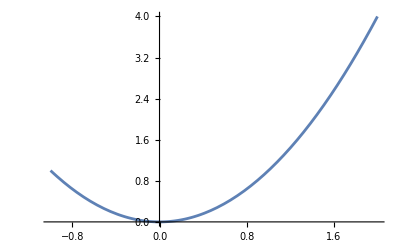

```mathematica
f[t_]:= t^2;
Plot[ f[t], {t, -1, 2}]
```

Notice that we use f[t], not just f; and the independent variable (t) along with the endpoints of the interval to plot appear in braces.  Instead of employing the name of the function, such as f[t], we can obtain the same results by using its definition, as follows:

```mathematica
Plot[t^2,{t, -1, 2}]
```

-Graphics-

To obtain the Plot template below using the Classroom Assistant, we open Basic Commands, click on the 2D tab, and then click on Plot under Visualizing Functions.  We then can tab from element to element.

```mathematica
Plot[function,{var,min,max}]
```

#### QRQ 11.1 Graph e^(sin(x)) from -3 to 3. Do not define a function for this expression but place the expression in the Plot command.

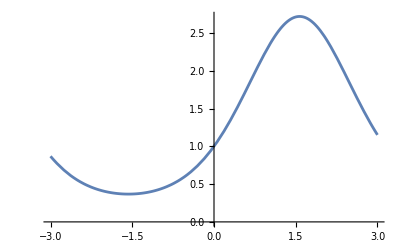

```mathematica
Plot[ⅇ^Sin[x],{x,-3,3}]
```

After braces containing the interval and a comma in the Plot command, an AxesLabel option generates axes labels, which should appear in all scientific graphics.  Following AxesLabel, the option has a hyphen (-) with a greater-than symbol (>) and braces containing the labels, which usually appear in quotation marks.  Mathematica changes -> that we type to a right arrow, →.  The command that follows plots the graph and labels the horizontal and vertical axes with t and y, respectively:

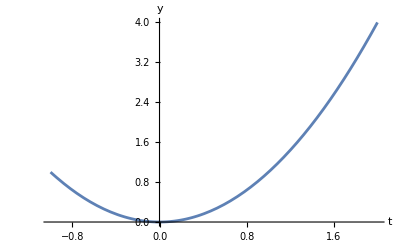

```mathematica
Plot[f[t],{t,-1,2},AxesLabel->{"t","y"}]
```

The Classroom Assistant provides various templates for AxesLabel under Basic Commands, 2D, Options, Axes & Frame.

#### QRQ 11.2 Adjust the answer to the previous QRQ to label the x and y axes. Also explore the suggestions given by Mathematica to alter the style of the plot in two different ways you find fun.

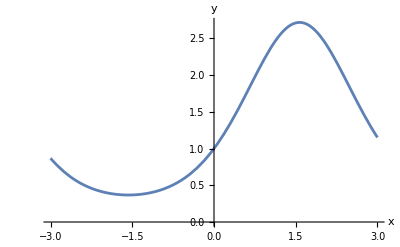

```mathematica
Plot[ⅇ^Sin[x],{x,-3,3}, AxesLabel->{"x","y"}]
```

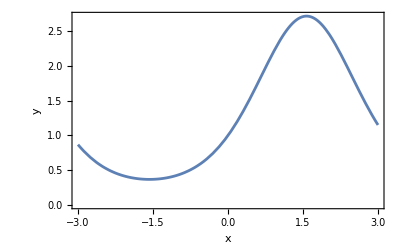

```mathematica
Show[%32,AxesStyle->Directive[RGBColor[1.,0.9034103913939117,0.18750286106660563],AbsoluteThickness[1]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

To plot several functions on the same graph using Plot, separate the functions by commas and place them in braces, such as follows:

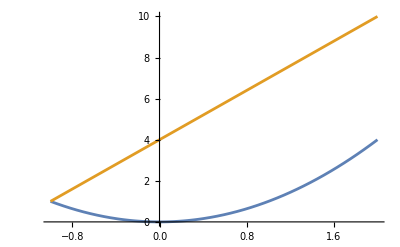

```mathematica
Plot[{f[t],3 t+4},{t,-1,2}]
```

If you don’t remember what f is, try:

```mathematica
?f
```

The word Global means that by default, all the variables and functions you defined are available to any other code you’re writing in a session. This is a major source of error, as it is easy to forget what we did even 10 min ago!

#### QRQ 11.3 Adjust the answer to the previous QRQ to plot e^(sin(x)) and sin(x) on the same graph.

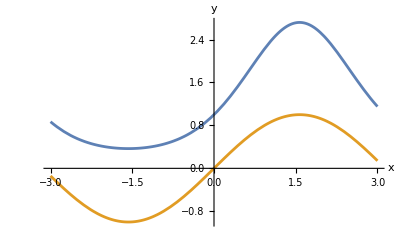

```mathematica
Plot[{ⅇ^Sin[x],Sin[x]},{x,-3,3}, AxesLabel->{"x","y"}]
```

## 12. Manipulate

Mathematica has a very powerful and simple   "Manipulate" command which allows user interaction with the output. Say you want to interactively change the frequency in the graph of a cosine function. The frequency is changed by making ω vary in cos(ωt).

```mathematica
Manipulate[
Plot[Cos[ω t], {t, -2 π, 2 π}],{ω, 0.5, 3}]
```

The Manipulate command just wraps around any command, providing a range for a parameter to vary inside the command. You can set the exact value of the parameter by clicking on the + sign. Try this.  
(note the  fourth entry ", 1" in the range {n, 1, 30, 1} of n,  insures it increments in whole number)

```mathematica
Manipulate[a (n!), {a, .5, 3}, {n, 1, 30, 1}]
```

#### QRQ 12.1 Write a Manipulate plotting the functions e^(sin(x)) and mx+b where the two parameters m and b can be manipulated in the intervals [.2 , 2], and [-1, 3] respectively. Use it to find, approximately, the equation of the tangent line to the graph at x=0. Use Calculus and Mathematica to compute its exact equation.

```mathematica
Manipulate[
Plot[{ⅇ^Sin[x], (m x+b)},{x, -10,10}],{m, .2, 2 },{b, -1, 3}]
```

tangent line to e^sin(x)= (y=1x+1) when x=0

## 13. Differentiation & Integration

As in calculus, Mathematica provides the prime notation for taking the derivative.  For example, consider the following function:
	 s(t) = -5.9t^2 +15t + 11
We define the function in Mathematica, as follows:

```mathematica
Clear[s, t]; (* Hygene, just in case we used these variables before *)
s[t_] := -5.9 t^2 + 15t + 11
```

The following prime notation returns the derivative function, 15 – 5.9t:

```mathematica
s'[t]
```

15-11.8 t

To evaluate the derivative at 1, which is s'(1) = 5.20, we call this derivative function at 1:

```mathematica
s'[1]
```

3.2

Alternatively, to avoid first defining a function, or if the function has more than one variable, we can employ the D command in Mathematica to compute the derivative.  The first argument is an expression for which we want the derivative, and the second is the independent variable.  Thus, to take the derivative of -5.9t^2 +15t + 11 with respect to t, we can employ the following command:

```mathematica
D[-5.9 t^2 + 15t + 11, t]
```

15-11.8 t

As indicated with the prime notation for the derivative, input to Mathematica can be quite natural.  Using the Classroom Assistant palette, we can request that Mathematica evaluate definite integrals and indefinite integrals using the notation of mathematics, such as with the following examples:

```mathematica
∫(-t^2+10t+24)ⅆt
```

24 t+5 t^2-t^3/3

```mathematica
∫_0^5 (-t^2+10t+24)ⅆt
```

610/3

Alternatively, as we discovered with Wolfram Alpha:

```mathematica
Integrate[-t^2+10t+24, t]
Integrate[-t^2+10t+24, {t, 0, 5}]
```

24 t+5 t^2-t^3/3

610/3

Warning! Most functions are not integrable, by humans or machines, in the sense of giving an explicit antiderivative:

```mathematica
Integrate[(Exp[x^3-3x]Sin[x]^2)/(x^3-4), x]
```

∫(ⅇ^(-3 x+x^3) Sin[x]^2)/(-4+x^3)ⅆx

However Mathematica will always be able to give you a numerical integral, using fancy numerical integration methods (Trapezoid rule, or Simpson rules and more sophisticated variations on those ...). The command is:

```mathematica
NIntegrate[(Exp[x^3-3x]Sin[x]^2)/(x^3-4), {x, -2, 1}]
```

-0.85933

#### QRQ 13.1 Give Mathematica code to do the following: a. Define the function f(x) = 2.9 sin(0.03x).

```mathematica
Clear[f,x,d]
f[x_]:= 2.9Sin[.03*x]
```

#### b. Evaluate the derivative of f at 35.

```mathematica
f'[35]
```

0.0432887

#### c. Define a function d(x) = f'(x) using the prime notation.

```mathematica
d[x_]:=f'[x]
```

#### d. Find the derivative of 2.9 sin(0.03x) using the D notation.

```mathematica
D[2.9 Sin[0.03x],x]
```

0.087 Cos[0.03 x]

#### e. Find the second derivative of 2.9 sin(0.03x) using the D notation (find how to do it in the Help menu). Does the double prime notation work? more primes?

```mathematica
D[2.9 Sin[0.03x],{x,2}]
```

-0.00261 Sin[0.03 x]

#### d. Write a Manipulate that gives the n^th derivative of 2.9 sin(0.03x) using the D notation, with n varying between 1 and 10 (in increments of 1). Could you have used the prime notation here?

```mathematica
Manipulate[D[2.9 Sin[0.03x],{x,n}],{n,1,10,1}]
```

#### QRQ 13.2 a. Plot sin^2(x) from 0 to 2π. (Careful - think about how you'd enter sin^2(x) on a calculator...)

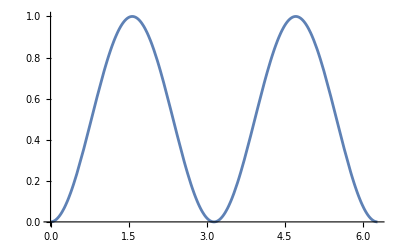

```mathematica
Plot[Sin[x]^2, {x,0,2π}]
```

#### b. Obtain the indefinite integral of sin^2(x).

```mathematica
Integrate[Sin[x]^2,x]
```

x/2-1/4 Sin[2 x]

#### c. Obtain the definite integral of sin^2(x) from 0 to 2π.

```mathematica
Integrate[Sin[x]^2,{x,0,2π}]
```

π

#### d. In a Manipulate, obtain the definite integral of sin^2(ωx) from 0 to 2π, for ω varying between .2 and 2

```mathematica
Manipulate[Integrate[Sin[ω x]^2,{x,0,2π}],{ω, .2,2}]
```

### QRQ 13.3 Find the definite integral of Sin(x^3-3 x +2) for x in [-1, 2]

```mathematica
Integrate[Sin[x^3-3 x +2], {x,-1,2}]
```

∫_-1^2 Sin[2-3 x+x^3]ⅆx

## 14. Solving Equations

Representing differential equations in Mathematica requires that we be able to represent equalities.  To avoid confusion with the assignment equal sign (=), Mathematica uses a double-equal sign (==) for equality in an equation.  Thus, we write the mathematical equation y = 5x + 3 as y == 5x + 3 in Mathematica.  
There are several ways to solve algebraic equations in Mathematica. The most common is using the command Solve:

```mathematica
Solve[3 x^2 - 6==2, x ]
```

Other commands that solve algebraic equations are NSolve, Reduce, FindRoots.

#### QRQ 14.1 Solve the equations i) x^3+x =0 ii) x^3+x -.2 =0 , asking for only the real solutions iii) x^3+Sin[x] -.2 =0 , asking for the solution nearest to -ⅈ

```mathematica
Solve[ x^3+x ==0, x]
Solve[x^3+x -.2 ==0,x, Reals]
Solve[x^3+Sin[x]-.2 ==0,x ,i]
```

{{x→0},{x→-ⅈ},{x→ⅈ}}

{{x→0.19283}}

### Differential Equations

We can employ the Mathematica function DSolve to solve a differential equation or a system of differential equations.  For example, suppose we wish to solve the differential equation F'(t) = -t^2 + 10t + 24 with initial condition F(0) = 30.  With braces surrounding these equations and double-equal signs to express the equality, we also indicate that we want to solve for F(t) and t is the independent variable, as follows:

```mathematica
Clear[t];
DSolve[{F'[t] ==  10 F[t] -t^2 + 24, F[0] == 30}, F[t], t]
```

{{F[t]→1/500 (-1199+16199 ⅇ^(10 t)+10 t+50 t^2)}}

#### QRQ 14.2 i) Solve the differential equation P'(t) = 0.1P(t) with initial condition P(0) = 100 , using Mathematica. ii) Graph the solution for t in [0, 20] and hover over the graph to estimate P(19). Then give the value to 3 digits of accuracy. How close were you in your estimate? Can you get more digits of accuracy?

```mathematica
Clear[P,t]
DSolve[{P'[t] ==  0.1 *P[t], P[0] == 100}, P[t], t]
```

{{P[t]→100. ⅇ^(0.1 t)}}

{{P[t]→100. ⅇ^(0.1 t)}}

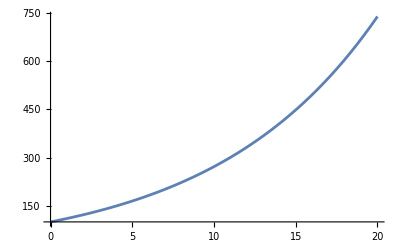

```mathematica
{{P[t]->100. ⅇ^(0.1 t)}}
Plot[100. ⅇ^(0.1 t),{t,0,20}]
Manipulate[100. ⅇ^(0.1 t),{t,0,20}]
```

P(19)=668.589